```mathematica
data={l0->0.4,l1->0.7,l2->1.2,l3->1.3,g->9.81,m1->0.148,m2->0.254,m3->0.276,m0->0.085}
```

{l0→0.4,l1→0.7,l2→1.2,l3→1.3,g→9.81,m1→0.148,m2→0.254,m3→0.276,m0→0.085}

```mathematica
eq1=l1 Cos[θ1]+l2 Cos[θ2]-l3 Cos[θ3]-l0
eq2=l1 Sin[θ1]+l2 Sin[θ2]-l3 Sin[θ3]
```

-l0+l1 Cos[θ1]+l2 Cos[θ2]-l3 Cos[θ3]

l1 Sin[θ1]+l2 Sin[θ2]-l3 Sin[θ3]

```mathematica
Solve[eq1==0,Cos[θ2]][[1]]
```

{Cos[θ2]→(l0-l1 Cos[θ1]+l3 Cos[θ3])/l2}

```mathematica
solcsθ2=Solve[{eq1,eq2}==0,{Cos[θ2],Sin[θ2]}][[1]]
```

{Cos[θ2]→(l0-l1 Cos[θ1]+l3 Cos[θ3])/l2,Sin[θ2]→(-l1 Sin[θ1]+l3 Sin[θ3])/l2}

```mathematica
elimθ2=Simplify[Numerator[Together[(Cos[θ2]^2+Sin[θ2]^2-1)/.solcsθ2]]]
```

l0^2+l1^2-l2^2+l3^2-2 l0 l1 Cos[θ1]-2 l1 l3 Cos[θ1-θ3]+2 l0 l3 Cos[θ3]

```mathematica
(*eq3=Numerator[elimθ2]*)
```

```mathematica
(*Simplify[eq3]*)
```

```mathematica
eq4=TrigExpand[elimθ2]
```

l0^2+l1^2-l2^2+l3^2-2 l0 l1 Cos[θ1]+2 l0 l3 Cos[θ3]-2 l1 l3 Cos[θ1] Cos[θ3]-2 l1 l3 Sin[θ1] Sin[θ3]

```mathematica
subs={Cos[θ3]->(1-t^2)/(1+t^2),Sin[θ3]->2 t/(1+t^2)}
```

{Cos[θ3]→(1-t^2)/(1+t^2),Sin[θ3]→(2 t)/(1+t^2)}

```mathematica
eq5=Collect[Numerator[Together[eq4/.subs]],t]
```

l0^2+l1^2-l2^2+2 l0 l3+l3^2-2 l0 l1 Cos[θ1]-2 l1 l3 Cos[θ1]+t^2 (l0^2+l1^2-l2^2-2 l0 l3+l3^2-2 l0 l1 Cos[θ1]+2 l1 l3 Cos[θ1])-4 l1 l3 t Sin[θ1]

```mathematica
solt=Solve[eq5==0,t]
```

{{t→(4 l1 l3 Sin[θ1]-√(-4 (l0^2+l1^2-l2^2+2 l0 l3+l3^2-2 l0 l1 Cos[θ1]-2 l1 l3 Cos[θ1]) (l0^2+l1^2-l2^2-2 l0 l3+l3^2-2 l0 l1 Cos[θ1]+2 l1 l3 Cos[θ1])+16 l1^2 l3^2 Sin[θ1]^2))/(2 (l0^2+l1^2-l2^2-2 l0 l3+l3^2-2 l0 l1 Cos[θ1]+2 l1 l3 Cos[θ1]))},{t→(4 l1 l3 Sin[θ1]+√(-4 (l0^2+l1^2-l2^2+2 l0 l3+l3^2-2 l0 l1 Cos[θ1]-2 l1 l3 Cos[θ1]) (l0^2+l1^2-l2^2-2 l0 l3+l3^2-2 l0 l1 Cos[θ1]+2 l1 l3 Cos[θ1])+16 l1^2 l3^2 Sin[θ1]^2))/(2 (l0^2+l1^2-l2^2-2 l0 l3+l3^2-2 l0 l1 Cos[θ1]+2 l1 l3 Cos[θ1]))}}

```mathematica
valt=Flatten[solt/.data/.{θ1->π/4}]
```

{t→0.102977,t→3.32449}

```mathematica
valθ3={θ3->2*ArcTan[t/.valt[[1]]],θ3->2*ArcTan[t/.valt[[2]]]}
```

{θ3→0.205231,θ3→2.55721}

```mathematica
th2va=(ArcTan[Cos[θ2]/.solcsθ2,Sin[θ2]/.solcsθ2])/.data/.{θ1->π/4}/.valθ3[[1]]
th2vb=(ArcTan[Cos[θ2]/.solcsθ2,Sin[θ2]/.solcsθ2])/.data/.{θ1->π/4}/.valθ3[[2]]
```

-0.192897

2.95534

```mathematica
br1={θ1->π/4,valθ3[[1]],θ2->th2va}
br2={θ1->π/4,valθ3[[2]],θ2->th2vb}
```

{θ1→π/4,θ3→0.205231,θ2→-0.192897}

{θ1→π/4,θ3→2.55721,θ2→2.95534}

```mathematica
p1={0,0}
p2={l1 Cos[θ1],l1 Sin [θ1]}/.data/.br1
p3=p2+{l2 Cos[θ2],l2 Sin[θ2]}/.data/.br1
p4={l0,0}/.data
p5=p4+{l3 Cos[θ3],l3 Sin[θ3]}/.data/.br1
```

{0,0}

{0.494975,0.494975}

{1.67272,0.264931}

{0.4,0}

{1.67272,0.264931}

```mathematica
line1=Graphics[Line[{p1,p2}]];
line2=Graphics[Line[{p2,p3}]];
line3=Graphics[Line[{p1,p4}]];
line4=Graphics[Line[{p4,p5}]];
```

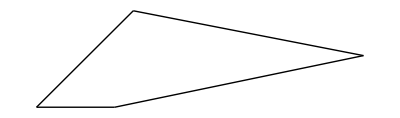

```mathematica
Show[{line1,line2,line3,line4}]
```

```mathematica
p1a={0,0}
p2a={l1 Cos[θ1],l1 Sin [θ1]}/.data/.br2
p3a=p2+{l2 Cos[θ2],l2 Sin[θ2]}/.data/.br2
p4a={l0,0}/.data
p5a=p4+{l3 Cos[θ3],l3 Sin[θ3]}/.data/.br2
```

{0,0}

{0.494975,0.494975}

{-0.684272,0.717185}

{0.4,0}

{-0.684272,0.717185}

```mathematica
line1a=Graphics[Line[{p1a,p2a}]];
line2a=Graphics[Line[{p2a,p3a}]];
line3a=Graphics[Line[{p1a,p4a}]];
line4a=Graphics[Line[{p4a,p5a}]];
```

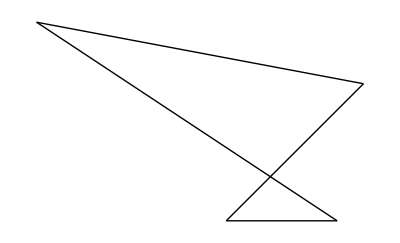

```mathematica
Show[{line1a,line2a,line3a,line4a}]
```

```mathematica
eq1t=eq1/.{θ1->θ1[t],θ2->θ2[t],θ3->θ3[t]}
```

-l0+l1 Cos[θ1[t]]+l2 Cos[θ2[t]]-l3 Cos[θ3[t]]

```mathematica
deq1=D[eq1t,t]
```

-l1 Sin[θ1[t]] θ1'[t]-l2 Sin[θ2[t]] θ2'[t]+l3 Sin[θ3[t]] θ3'[t]

```mathematica
Solve[deq1==0,θ1'[t]]
```

{{θ1'[t]→-(Csc[θ1[t]] (l2 Sin[θ2[t]] θ2'[t]-l3 Sin[θ3[t]] θ3'[t]))/l1}}

```mathematica
eq2t=eq2/.{θ1->θ1[t],θ2->θ2[t],θ3->θ3[t]}
```

l1 Sin[θ1[t]]+l2 Sin[θ2[t]]-l3 Sin[θ3[t]]

```mathematica
deq2=D[eq2t,t]
```

l1 Cos[θ1[t]] θ1'[t]+l2 Cos[θ2[t]] θ2'[t]-l3 Cos[θ3[t]] θ3'[t]

```mathematica
Solve[deq2==0,θ2'[t]]
```

{{θ2'[t]→-(Sec[θ2[t]] (l1 Cos[θ1[t]] θ1'[t]-l3 Cos[θ3[t]] θ3'[t]))/l2}}

```mathematica
Theta= {θ1->θ1[t],θ2->θ2[t],θ3->θ3[t]}
```

{θ1→θ1[t],θ2→θ2[t],θ3→θ3[t]}

```mathematica
cm1 = {l1/2*Cos[θ1],l1/2*Sin[θ1]}/.Theta
```

{1/2 l1 Cos[θ1[t]],1/2 l1 Sin[θ1[t]]}

```mathematica
cm2={l1*Cos[θ1]+l2/2*Cos[θ2],l1*Sin[θ1]+l2/2*Sin[θ2]}/.Theta
```

{l1 Cos[θ1[t]]+1/2 l2 Cos[θ2[t]],l1 Sin[θ1[t]]+1/2 l2 Sin[θ2[t]]}

```mathematica
cm3= {l0+(1/2)*l3*Cos[θ3],(1/2)l3*Sin[θ3]}/.Theta
```

{l0+1/2 l3 Cos[θ3[t]],1/2 l3 Sin[θ3[t]]}

```mathematica
vcm1 = D[cm1,t]
vcm2= D[cm2,t]
vcm3 = D[cm3,t]
```

{-1/2 l1 Sin[θ1[t]] θ1'[t],1/2 l1 Cos[θ1[t]] θ1'[t]}

{-l1 Sin[θ1[t]] θ1'[t]-1/2 l2 Sin[θ2[t]] θ2'[t],l1 Cos[θ1[t]] θ1'[t]+1/2 l2 Cos[θ2[t]] θ2'[t]}

{-1/2 l3 Sin[θ3[t]] θ3'[t],1/2 l3 Cos[θ3[t]] θ3'[t]}

```mathematica
I1= 1/12*m1*l1^2;
I2 = 1/12*m2*l2^2;
I3 =1/12*m3*l3^2;
```

```mathematica
ke1 = Simplify[ 1/2*m1*vcm1.vcm1+1/2*I1*θ1'[t]^2]
```

1/6 l1^2 m1 θ1'[t]^2

```mathematica
ke2 = Simplify[ 1/2*m2*vcm2.vcm2+1/2*I2*θ2'[t]^2]
```

1/6 m2 (3 l1^2 θ1'[t]^2+3 l1 l2 Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+l2^2 θ2'[t]^2)

```mathematica
ke3 = Simplify[ 1/2*m3*vcm3.vcm3+1/2*I3*θ3'[t]^2]
```

1/6 l3^2 m3 θ3'[t]^2

```mathematica
T = Simplify[ke1+ke2+ke3]
q1 = D[D[T,θ1'[t]],t]
q2 = D[D[T,θ2'[t]],t]
q3 = D[D[T,θ3'[t]],t]
```

1/6 (l1^2 (m1+3 m2) θ1'[t]^2+3 l1 l2 m2 Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+l2^2 m2 θ2'[t]^2+l3^2 m3 θ3'[t]^2)

1/6 (-3 l1 l2 m2 Sin[θ1[t]-θ2[t]] (θ1'[t]-θ2'[t]) θ2'[t]+2 l1^2 (m1+3 m2) θ1''[t]+3 l1 l2 m2 Cos[θ1[t]-θ2[t]] θ2''[t])

1/6 (-3 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t] (θ1'[t]-θ2'[t])+3 l1 l2 m2 Cos[θ1[t]-θ2[t]] θ1''[t]+2 l2^2 m2 θ2''[t])

1/3 l3^2 m3 θ3''[t]

```mathematica
row1={Coefficient[q1,θ1''[t]],Coefficient[q1,θ2''[t]],Coefficient[q1,θ3''[t]]}
row2={Coefficient[q2,θ1''[t]],Coefficient[q2,θ2''[t]],Coefficient[q2,θ3''[t]]}
row3={Coefficient[q3,θ1''[t]],Coefficient[q3,θ2''[t]],Coefficient[q3,θ3''[t]]}
```

{1/3 l1^2 (m1+3 m2),1/2 l1 l2 m2 Cos[θ1[t]-θ2[t]],0}

{1/2 l1 l2 m2 Cos[θ1[t]-θ2[t]],(l2^2 m2)/3,0}

{0,0,(l3^2 m3)/3}

```mathematica
M={row1,row2,row3}
```

{{1/3 l1^2 (m1+3 m2),1/2 l1 l2 m2 Cos[θ1[t]-θ2[t]],0},{1/2 l1 l2 m2 Cos[θ1[t]-θ2[t]],(l2^2 m2)/3,0},{0,0,(l3^2 m3)/3}}

```mathematica
MatrixForm[M]
```

(1/3 l1^2 (m1+3 m2) | 1/2 l1 l2 m2 Cos[θ1[t]-θ2[t]] | 0
1/2 l1 l2 m2 Cos[θ1[t]-θ2[t]] | (l2^2 m2)/3 | 0
0 | 0 | (l3^2 m3)/3)

```mathematica
Dimensions[M]
```

{3,3}

```mathematica
Simplify[Transpose[M]-M]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
q={θ1[t],θ2[t],θ3[t]}
qd={θ1'[t],θ2'[t],θ3'[t]}
```

{θ1[t],θ2[t],θ3[t]}

{θ1'[t],θ2'[t],θ3'[t]}

```mathematica
Cor=ConstantArray[0,{3,3}];
```

```mathematica
For[ii=1,ii<=3,ii++,
For[jj=1,jj<=3,jj++,
For[kk=1,kk<=3,kk++,
Cor[[ii,jj]]+=0.5(D[M[[ii,jj]],q[[kk]]]+D[M[[ii,kk]],q[[jj]]]-D[M[[kk,jj]],q[[ii]]])*qd[[kk]];
];
];
];
```

```mathematica
check=D[M,t]-2*Cor
```

{{0.,-1/2 l1 l2 m2 Sin[θ1[t]-θ2[t]] (θ1'[t]-θ2'[t])-2 (0.+0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ2'[t]),0.},{-2 (0.-0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t])-1/2 l1 l2 m2 Sin[θ1[t]-θ2[t]] (θ1'[t]-θ2'[t]),0.,0.},{0.,0.,0.}}

```mathematica
Simplify[check+Transpose[check]]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
η={eq1,eq2}/.{θ1->θ1[t],θ2->θ2[t],θ3->θ3[t]}
```

{-l0+l1 Cos[θ1[t]]+l2 Cos[θ2[t]]-l3 Cos[θ3[t]],l1 Sin[θ1[t]]+l2 Sin[θ2[t]]-l3 Sin[θ3[t]]}

```mathematica
Jηq=D[η,{q}];
MatrixForm[Jηq]
```

(-l1 Sin[θ1[t]] | -l2 Sin[θ2[t]] | l3 Sin[θ3[t]]
l1 Cos[θ1[t]] | l2 Cos[θ2[t]] | -l3 Cos[θ3[t]])

```mathematica
v1 = m1*g*cm1[[2]]+m2*g*cm2[[2]]+m3*g*cm3[[2]]
```

1/2 g l1 m1 Sin[θ1[t]]+g m2 (l1 Sin[θ1[t]]+1/2 l2 Sin[θ2[t]])+1/2 g l3 m3 Sin[θ3[t]]

```mathematica
G= D[v1,{q}]
```

{1/2 g l1 m1 Cos[θ1[t]]+g l1 m2 Cos[θ1[t]],1/2 g l2 m2 Cos[θ2[t]],1/2 g l3 m3 Cos[θ3[t]]}

```mathematica
A =Jηq.Inverse[M].Transpose[Jηq] ;
MatrixForm[A]
```

(-l2 Sin[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-l1 Sin[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Sin[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2) | l2 Cos[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)
-l1 ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) Sin[θ1[t]]-l2 (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) Sin[θ2[t]]-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2) | l2 Cos[θ2[t]] (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))

```mathematica
Dimensions[A]
```

{2,2}

```mathematica
Dimensions[Jηq]
```

{2,3}

```mathematica
qnc= {0,0,0};
f= qnc - Cor.qd - G;
MatrixForm[f]
```

(0.-1/2 g l1 m1 Cos[θ1[t]]-g l1 m2 Cos[θ1[t]]-θ2'[t] (0.+0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ2'[t])
0.-1/2 g l2 m2 Cos[θ2[t]]-θ1'[t] (0.-0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t])
0.-1/2 g l3 m3 Cos[θ3[t]])

```mathematica
Jηqd = D[Jηq,t];
```

```mathematica
λ = -(Inverse[A].(Jηqd.qd+Jηq.Inverse[M].f));
MatrixForm[λ]
```

(-((l2 Cos[θ2[t]] (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) ((l3 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) (0.-1/2 g l3 m3 Cos[θ3[t]]) Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)-l1 Cos[θ1[t]] θ1'[t]^2+((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (0.-1/2 g l2 m2 Cos[θ2[t]]-θ1'[t] (0.-0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t]))-l2 Cos[θ2[t]] θ2'[t]^2+(-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) (0.-1/2 g l1 m1 Cos[θ1[t]]-g l1 m2 Cos[θ1[t]]-θ2'[t] (0.+0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ2'[t]))+l3 Cos[θ3[t]] θ3'[t]^2))/(-((-l1 ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) Sin[θ1[t]]-l2 (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) Sin[θ2[t]]-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (l2 Cos[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l2 Cos[θ2[t]] (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (-l2 Sin[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-l1 Sin[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Sin[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))-((-l2 Cos[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-l1 Cos[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (-(l3 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] (0.-1/2 g l3 m3 Cos[θ3[t]]))/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)-l1 Sin[θ1[t]] θ1'[t]^2+(-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (0.-1/2 g l2 m2 Cos[θ2[t]]-θ1'[t] (0.-0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t]))-l2 Sin[θ2[t]] θ2'[t]^2+((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) (0.-1/2 g l1 m1 Cos[θ1[t]]-g l1 m2 Cos[θ1[t]]-θ2'[t] (0.+0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ2'[t]))+l3 Sin[θ3[t]] θ3'[t]^2))/(-((-l1 ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) Sin[θ1[t]]-l2 (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) Sin[θ2[t]]-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (l2 Cos[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l2 Cos[θ2[t]] (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (-l2 Sin[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-l1 Sin[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Sin[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))
-((l1 ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) Sin[θ1[t]]+l2 (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) Sin[θ2[t]]+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) ((l3 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) (0.-1/2 g l3 m3 Cos[θ3[t]]) Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)-l1 Cos[θ1[t]] θ1'[t]^2+((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (0.-1/2 g l2 m2 Cos[θ2[t]]-θ1'[t] (0.-0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t]))-l2 Cos[θ2[t]] θ2'[t]^2+(-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) (0.-1/2 g l1 m1 Cos[θ1[t]]-g l1 m2 Cos[θ1[t]]-θ2'[t] (0.+0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ2'[t]))+l3 Cos[θ3[t]] θ3'[t]^2))/(-((-l1 ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) Sin[θ1[t]]-l2 (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) Sin[θ2[t]]-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (l2 Cos[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l2 Cos[θ2[t]] (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (-l2 Sin[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-l1 Sin[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Sin[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))-((-l2 Sin[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-l1 Sin[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Sin[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (-(l3 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] (0.-1/2 g l3 m3 Cos[θ3[t]]))/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)-l1 Sin[θ1[t]] θ1'[t]^2+(-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (0.-1/2 g l2 m2 Cos[θ2[t]]-θ1'[t] (0.-0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t]))-l2 Sin[θ2[t]] θ2'[t]^2+((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) (0.-1/2 g l1 m1 Cos[θ1[t]]-g l1 m2 Cos[θ1[t]]-θ2'[t] (0.+0.5 l1 l2 m2 Sin[θ1[t]-θ2[t]] θ2'[t]))+l3 Sin[θ3[t]] θ3'[t]^2))/(-((-l1 ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))) Sin[θ1[t]]-l2 (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) Sin[θ2[t]]-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (l2 Cos[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))-(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]] Sin[θ3[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l2 Cos[θ2[t]] (-(l1^2 l2 l3^2 m2 m3 Cos[θ1[t]] Cos[θ1[t]-θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Cos[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+l1 Cos[θ1[t]] ((l1 l2^2 l3^2 m2 m3 Cos[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Cos[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Cos[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)) (-l2 Sin[θ2[t]] ((l1^2 l2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ1[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-(l2 (1/9 l1^2 l3^2 m1 m3+1/3 l1^2 l3^2 m2 m3) Sin[θ2[t]])/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))-l1 Sin[θ1[t]] (-(l1 l2^2 l3^2 m2 m3 Sin[θ1[t]])/(9 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))+(l1 l2^2 l3^2 m2 m3 Cos[θ1[t]-θ2[t]] Sin[θ2[t]])/(6 (1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2)))+(l3^2 (1/9 l1^2 l2^2 m1 m2+1/3 l1^2 l2^2 m2^2-1/4 l1^2 l2^2 m2^2 Cos[θ1[t]-θ2[t]]^2) Sin[θ3[t]]^2)/(1/27 l1^2 l2^2 l3^2 m1 m2 m3+1/9 l1^2 l2^2 l3^2 m2^2 m3-1/12 l1^2 l2^2 l3^2 m2^2 m3 Cos[θ1[t]-θ2[t]]^2))))

```mathematica
qdd = Inverse[M].f - Inverse[M].Transpose[Jηq].Inverse[A].(Jηqd.qd+Jηq.Inverse[M].f);
MatrixForm[qdd]
```

```mathematica
qdata= Simplify[qdd /.data];
```

```mathematica
Dimensions[qdata]
```

{3}

```mathematica
br1
```

{θ1→π/4,θ3→0.205231,θ2→-0.192897}

```mathematica
qdatachop=Chop[qdata];
```

```mathematica
qdatachop/.{θ1[t]->π/4,θ3[t]->0.20523052222953653,θ2[t]->-0.19289741126288126}
```

{-0.941836 (9.48039+0.529582 θ1'[t]^2+1.77359 θ2'[t]^2-1.7293 θ3'[t]^2),-0.941836 (7.81926-0.89935 θ1'[t]^2-1.06163 θ2'[t]^2+1.54057 θ3'[t]^2),-0.941836 (10.9228-0.213348 θ1'[t]^2-0.484549 θ2'[t]^2+0.532046 θ3'[t]^2)}

```mathematica
tf=5;
s1=NDSolve[{{θ1''[t],θ2''[t],θ3''[t]}-{qdatachop[[1]],qdatachop[[2]],qdatachop[[3]]}=={0,0,0},θ1[0]==π/4,θ2[0]==-0.1928,θ3[0]==0.2052,θ1'[0]==0,θ2'[0]==0,θ3'[0]==0},{θ1,θ2,θ3},{t,0,tf}]
```

{{θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…],θ3→InterpolatingFunction[…]}}

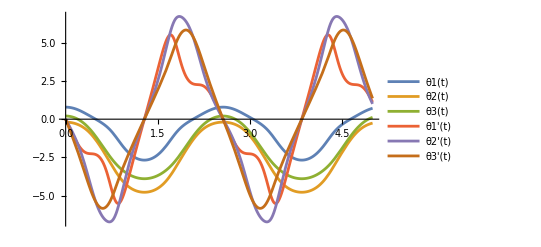

```mathematica
Plot[Evaluate[{θ1[t],θ2[t],θ3[t],θ1'[t],θ2'[t],θ3'[t]}/. s1],{t,0,tf},PlotStyle->Automatic,PlotLegends->{θ1[t],θ2[t],θ3[t],θ1'[t],θ2'[t],θ3'[t]}]
```

```mathematica
th1valsx=(θ1["ValuesOnGrid"]/.s1)[[1]];
th2valsx=(θ2["ValuesOnGrid"]/.s1)[[1]];
th3valsx=(θ3["ValuesOnGrid"]/.s1)[[1]];
th1dvalsx=(θ1'["ValuesOnGrid"]/.s1)[[1]];
th2dvalsx=(θ2'["ValuesOnGrid"]/.s1)[[1]];
th3dvalsx=(θ3'["ValuesOnGrid"]/.s1)[[1]];
th1ddvalsx=(θ1''["ValuesOnGrid"]/.s1)[[1]];
th2ddvalsx=(θ2''["ValuesOnGrid"]/.s1)[[1]];
th3ddvalsx=(θ3''["ValuesOnGrid"]/.s1)[[1]];
```

```mathematica
lenx=Length[th1valsx]
```

390

```mathematica
ndsolresultsx=Table[Inner[Rule,{θ1[t],θ2[t],θ3[t],θ1'[t],θ2'[t],θ3'[t],θ1''[t],θ2''[t],θ3''[t]},{th1valsx[[ii]],th2valsx[[ii]],th3valsx[[ii]],th1dvalsx[[ii]],th2dvalsx[[ii]],th3dvalsx[[ii]],th1ddvalsx[[ii]],th2ddvalsx[[ii]],th3ddvalsx[[ii]]},List],{ii,1,lenx}]
```

```mathematica
TEx=(T+v1)/.data
```

0.508158 Sin[θ1[t]]+2.49174 (0.7 Sin[θ1[t]]+0.6 Sin[θ2[t]])+1.75991 Sin[θ3[t]]+1/6 (0.4459 θ1'[t]^2+0.64008 Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+0.36576 θ2'[t]^2+0.46644 θ3'[t]^2)

```mathematica
TEvalsx=TE/.ndsolresultsx;
```

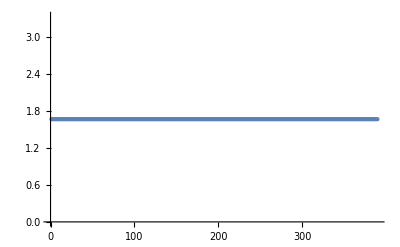

```mathematica
ListPlot[TEvalsx]
```

```mathematica
energycheck=((TEvalsx-TEvalsx[[1]])/TEvalsx[[1]])*100;
```

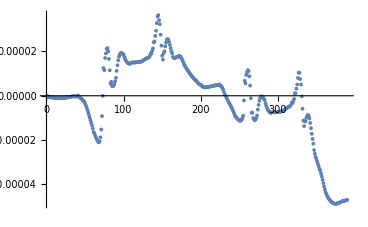

```mathematica
ListPlot[energycheck]
```